# MATH299M/CMSC389W - Visualization through Mathematica Week 8: Plotting III: PolarPlot and ParametricPlot

Here we introduce two more plotting tools - PolarPlot and ParametricPlot. ParametricPlot is more powerful, so we will start with PolarPlot, as it will be a good opportunity to review polar form.

PolarPlot

PolarPlot takes two arguments. The first is a function for the radius in terms of some variable, and the second is a domain tuple for that variable, generally chosen to be θ, and then it draws the function (r(θ),θ) plotted on a polar graph. Recall that a polar graph is one where the grid lines are concentric circles with perpendicular radial lines rather than an xy grid - the axes we are using, instead of x from -∞ to ∞ and y from -∞ to ∞ are r from 0 to ∞ and θ from 0 to 2π, radius and angle, respectively. You could also think of it as r from -∞ to ∞ ad θ from 0 to π, both cover the negative direction - in general with PolarPlot you can have any value of r and θ, so you can combine these notions of the opposite direction being represented by a negative radius and by an angle between π and 2π, and also you can utilize values of θ above 2π and below 0 to wrap around the origin more, although on principle you should be able to draw every polar curve you can imagine on the domain [0,∞)x[0,2π).

A circle in polar form is extremely simple - the radius is constant and theta swings through all angles.

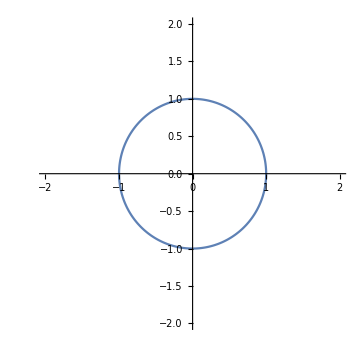

```mathematica
PolarPlot[1,{θ,0,2π},PlotRange->2,AspectRatio->1,ImageSize->Medium]
```

The polar flowers are always a go-to:

```mathematica
Manipulate[PolarPlot[Sin[n θ],{θ,0,2π},PlotRange->2,AspectRatio->1,ImageSize->Medium],{{n,3},1,10,1}]
```

Something crazy to see, and very illuminating as to how these flowers are actually drawn, is if you let n be any real number:

```mathematica
Manipulate[PolarPlot[Sin[n θ],{θ,0,2π},PlotRange->2,AspectRatio->1,ImageSize->Medium],{{n,3},-10,10}]
```

The trig functions do simple things on polar graphs - why this is is important and interesting, and these tools are particularly conducive to understanding why. I insist that you play with these yourself and build an understanding of how polar flowers, cardioids, and conics are drawn in polar form. I cheated a little bit adding a tiny bit (denoted epsilon ϵ) to the start and end of the θ interval - otherwise we have dividing by zero problems and errors get thrown (which function(s) is this a problem for?).

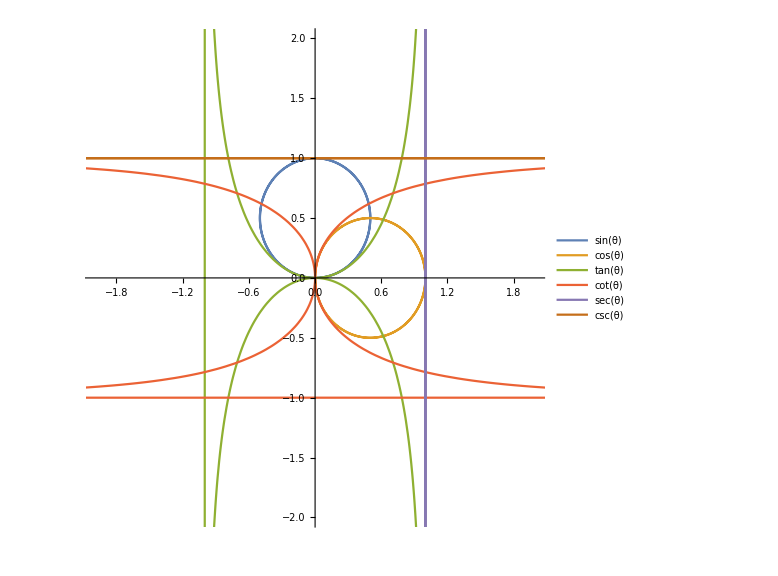

```mathematica
ϵ=.0001;
PolarPlot[{Sin[θ],Cos[θ],Tan[θ],Cot[θ],Sec[θ],Csc[θ]},{θ,0+ϵ,2π-ϵ},PlotRange->2,AspectRatio->1,ImageSize->Large,PlotLegends->"Expressions"]
```

ParametricPlot

ParametricPlot is one of my favorite tools in Mathematica - it’s extremely powerful. In case you’ve never seen parametric curves before (multivariate calculus is usually the first time you see such a thing), the idea is that you draw an arbitrary curve in the plane and parameterize it with a real number t, that is, you have a function f(t) that returns a coordinate pair (x(t),y(t)) that varies with t. ParameticPlot takes two or three arguments, the first is a tuple in terms of t that describes the path in the plane, and the second is a tuple that gives the domain of t, and of course “t” can be any variable, and we have the normal Plot options, if we don’t use the third argument. Notice that in this case there is only one dimension of domain as for a parameterized line it can be fully described as a function from ℝ to ℝ^2. If we use the third argument, it’s another domain tuple, so actually we may construct a parametric function {x(t,s),y(t,s)} that swings through all points (x,y) ∈ ℝ^2 wrt to all specified values of s and t (or whatever you call these variables, often it’s nice to call them θ and r if you’re doing something polar).

Let’s see something you can’t do with a Plot, plotting something that isn’t a function, that is, doesn’t pass the vertical line test:

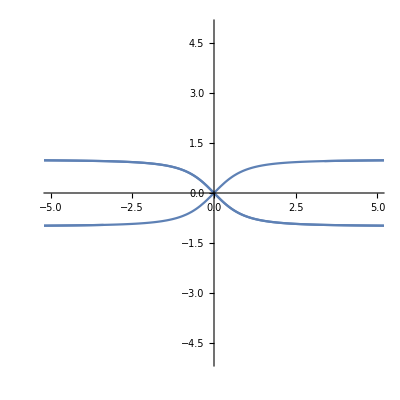

```mathematica
ParametricPlot[{Tan[t],Sin[t]},{t,-5,5},PlotRange->5,AspectRatio->1]
```

If you want a normal function, you can type {t,f[t]} for {x(t),y(t)}, which is equivalent to using Plot on f[t] where t is the dependent variable. Similarly if we make the second element of the tuple just t and the first f[t], then it’s like we’re plotting on the graph x = y, like what Plot does but with the axes flipped.

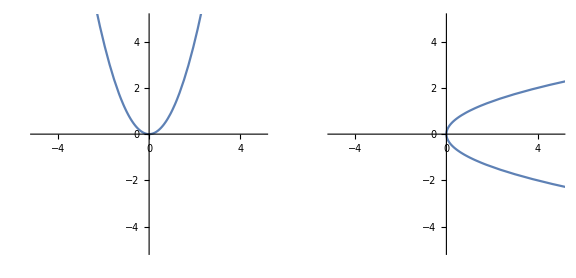

```mathematica
GraphicsGrid[{{ParametricPlot[{t,t^2},{t,-5,5},PlotRange->5,AspectRatio->1],ParametricPlot[{t^2,t},{t,-5,5},PlotRange->5,AspectRatio->1]}},ImageSize->Large]
```

ParametricPlot is great for Polar drawings as you can parameterize the radius and angle:

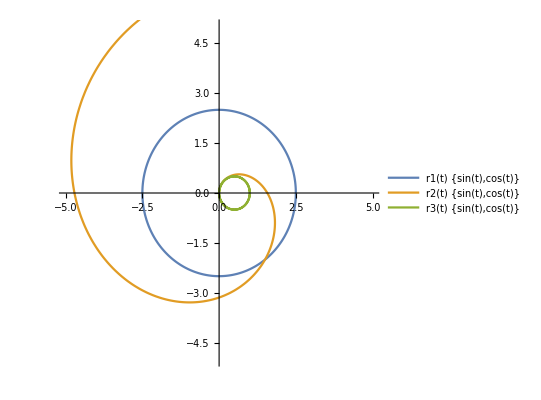

```mathematica
r1[t_]:=2.5; (* Constant Radius *)
r2[t_]:=t; (* Increasing Radius *)
r3[t_]:=Sin[t]; (* Sinusoidal Radius *)
ParametricPlot[{r1[t]{Sin[t],Cos[t]},r2[t]{Sin[t],Cos[t]},r3[t]{Sin[t],Cos[t]}},{t,0,2π},PlotRange->5,AspectRatio->1,PlotLegends->"Expressions"]
```

ParametricPlot with two domain variables, possibly combined with this polar technique, is great for the objects we want to integrate over in Calculus II, like washers and wedges:

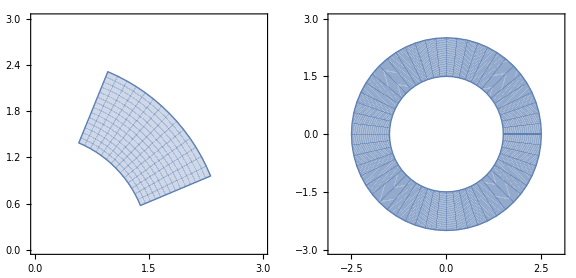

```mathematica
GraphicsGrid[{{ParametricPlot[r{Cos[θ],Sin[θ]},{r,1.5,2.5},{θ,π/8,(3π)/8},PlotRange->{{0,3},{0,3}},AspectRatio->1],
ParametricPlot[r{Cos[θ],Sin[θ]},{r,1.5,2.5},{θ,0,2π},PlotRange->3,AspectRatio->1]}},ImageSize->Large]
```

One more trick to show you is using Manipulate on the domain to control the drawing:

```mathematica
Manipulate[ParametricPlot[Sin[2θ]{Sin[θ],Cos[θ]},{θ,min,max},PlotRange->1.5,AspectRatio->1],{{min,0},-2π,0},{{max,π/8},0,2π}]
```

You now have at your disposal powerful tools to draw arbitrary curves in the plane!

## Ajeet Gary - University of Maryland Experimental Geometry Lab MATH299M/CMSC389W Fall 2018 October 7th, 2018